```mathematica
xdot = -mu*y + y*(x-x*y-y);
ydot = mu*x - x^2 + x*y - y^3;
sol = FullSimplify[Solve[{xdot == 0, ydot == 0}, {x,y},Reals]]
```

{{x→1/2 (mu-√(mu^2)),y→0},{x→1/2 (mu+√(mu^2)),y→0}}

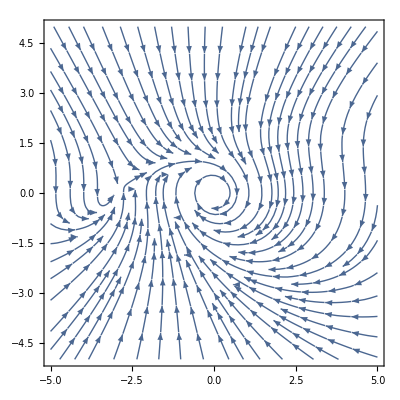

```mathematica
StreamPlot[{xdot, ydot}/.mu->-3, {x,-5,5}, {y,-5,5}]
```

```mathematica
J = {{D[xdot,x], D[xdot,y]},{D[ydot,x], D[ydot,y]}};
J00 = J/.{x->0, y->0};
Jmu0 = J/.{x->mu, y->0};
Eigenvalues[J00]
Eigenvalues[Jmu0]
```

{ⅈ mu,-ⅈ mu}

{mu,0}